```mathematica
f = lw+pw^3 (2/(n bc^4)+(b g)/(2 n bc^3))+pw (-g-2/(n bc^2)+(b g)/bc-(b g)/(2 n bc))
R = Solve[f==0,pw];
r1 = R[[1]][[1]];
r2 = R[[2]][[1]];
r3 = R[[3]][[1]];
(*Roots for free field case*)
rr1 = pw/.r1;
rr2 = pw/.r2;
rr3 =pw/.r3;
rb1 = Simplify[rr1,{g>0,r>0,n>0}];
rb2 = Simplify[rr2,{g>0,r>0,n>0}];
rb3 = Simplify[rr3,{g>0,r>0,n>0}];
Bc = b/.Solve[(√(g n (2-2 b √r)+b g √r+4 r))/(√(b g r^(3/2)+4 r^2))==0,b][[1]]
```

lw+(-g+(b g)/bc-2/(bc^2 n)-(b g)/(2 bc n)) pw+(2/(bc^4 n)+(b g)/(2 bc^3 n)) pw^3

(2 (g n+2 r))/(g (-1+2 n) √r)

```mathematica
Simplify[√(-(bc^2 (4+b bc g (1-2 n)+2 bc^2 g n))/(4+b bc g))+(√(-(bc^2 (4+b bc g (1-2 n)+2 bc^2 g n))/(4+b bc g)))/(√3)]
```

1/3 (3+√3) √(-(bc^2 (4+b bc g (1-2 n)+2 bc^2 g n))/(4+b bc g))

Plot order parameter for different n values in the present of actin-bands.

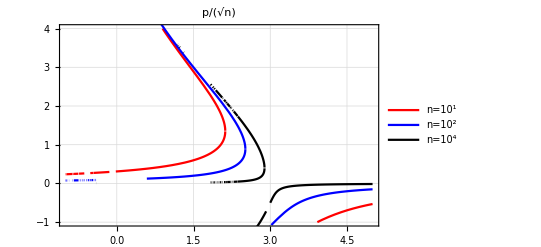

```mathematica
p1 = Plot[{Chop[{rb1,rb2,rb3}]/Sqrt[n]}/.lw-> 1/.n-> 10/.bc->3/.g-> 1,{b,-1,5},PlotStyle->{{Red},{Red},{Dashed}},PlotRange->{-1,4},PlotLegends-> {"n=10^1"},Frame->True,GridLines->Automatic];
p2 = Plot[{Chop[{rb1,rb2,rb3}]/Sqrt[n]}/.lw-> 1/.n-> 10^2/.bc->3/.g-> 1,{b,-1,5},PlotStyle->Blue,PlotLegends-> {"n=10^2"}];
p3 = Plot[{Chop[{rb1,rb2,rb3}]/Sqrt[n]}/.lw-> 1/.n-> 10^4/.bc->3/.g-> 1,{b,-1,5},PlotStyle->Black,PlotLegends-> {"n=10^4"}];
Show[p1,p2,p3,PlotLabel->Style[p/Sqrt[n] (λ = 1),18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

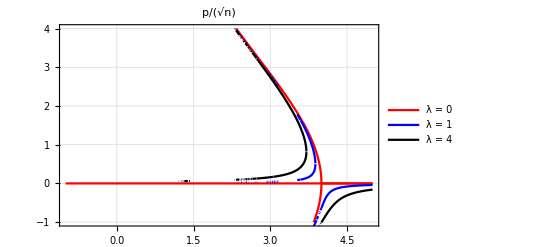

```mathematica
p1 = Plot[{Chop[{rb1,rb2,0}]/Sqrt[n]}/.lw-> 0/.n-> 10^4/.bc->4/.g-> 1,{b,-1,5},PlotStyle->{{Red},{Red},{Dashed}},PlotRange->{-1,4},PlotLegends-> {"λ = 0"},Frame->True,GridLines->Automatic];
p2 = Plot[{Chop[{rb1,rb2,rb3}]/Sqrt[n]}/.lw-> 1/.n-> 10^4/.bc->4/.g-> 1,{b,-1,5},PlotStyle->Blue,PlotLegends-> {"λ = 1"}];
p3 = Plot[{Chop[{rb1,rb2,rb3}]/Sqrt[n]}/.lw-> 4/.n-> 10^4/.bc->4/.g-> 1,{b,-1,5},PlotStyle->Black,PlotLegends-> {"λ = 4"}];
Show[p1,p2,p3,PlotLabel->Style[p/Sqrt[n] ,18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

Plot order parameter in function of actin band for different beta values

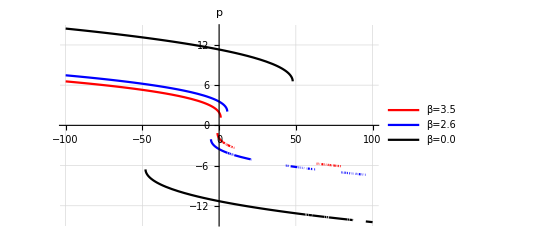

```mathematica
p1 =  Plot[{rb1/Sqrt[n],rb2/Sqrt[n]}/.g-> 1/.n->121/.b -> 3.5/.bc-> 4,{lw,-100,100},PlotStyle->Red,PlotRange->All,GridLines->Automatic,PlotLegends-> {"β=3.5"}];
p2 = Plot[{rb1/Sqrt[n],rb2/Sqrt[n]}/.g-> 1/.n->121/.b -> 2.6/.bc-> 4,{lw,-100,100},PlotStyle->Blue,PlotRange->All,GridLines->Automatic,PlotLegends-> {"β=2.6"}];
p3 = Plot[{rb1/Sqrt[n],rb2/Sqrt[n]}/.g-> 1/.n->121/.b -> 0/.bc-> 4,{lw,-100,100},PlotStyle->Black,PlotRange->All,GridLines->Automatic,PlotLegends-> {"β=0.0"}];
Show[p1,p2,p3,PlotLabel->Style[p,18],AxesLabel->{Style[λ,16]},LabelStyle->Directive[Bold]]
```

```mathematica
Plot3D[Chop[{rb1/bc,rb3/bc}]/.g-> 1/.n->121/.bc->4,{lw,0,8},{b,0,4},PlotRange->{0,15},AxesLabel->{Style[λ,16],Style[β,16]},PlotLabel->Style[p,18]]
```

-Graphics3D-

Critical beta (free-field) in function of n

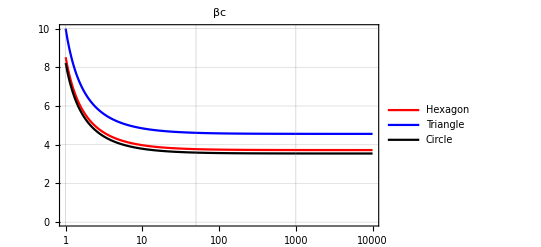

```mathematica
p1 = LogLinearPlot[{Bc/.r-> 1/(8 √3)/.g-> 1},{n,10^0,10^4},PlotStyle->Red,PlotRange->{0,10},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p2 = LogLinearPlot[{Bc/.r-> 1/(12 √3)/.g-> 1},{n,10^0,10^4},PlotStyle->Blue,PlotRange->{0,10},PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
p3 = LogLinearPlot[{Bc/.r-> 1/(4Pi)/.g-> 1},{n,10^0,10^4},PlotStyle->Black,PlotRange->{0,10},PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];
Show[p1,p2,p3,PlotLabel->Style[βc,18],AxesLabel->{Style[n,18]},LabelStyle->Directive[Bold]]
```

Plot order parameter in function of beta for different polygons and compare with numerical simulations

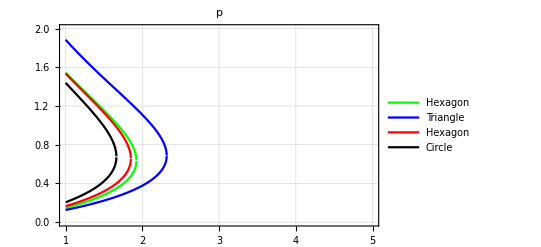

```mathematica
p1 = Plot[{{rr1,rr2,rr3}/(Sqrt[n/r])}/.lw-> 4b g/.n-> 100/.r-> 1/(8 √3)/.g-> 1,{b,1,5},PlotStyle->Green,PlotRange->{0,2},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p2 = Plot[{{rr1,rr2,rr3}/(Sqrt[n/r])}/.lw-> 4b g/.n-> 80/.r-> 1/(12 √3)/.g-> 1,{b,1,5},PlotStyle->Blue,PlotRange->{0,2},PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
p3 = Plot[{{rr1,rr2,rr3}/(Sqrt[n/r])}/.lw-> 4b g/.n-> 80/.r-> 1/(8 √3)/.g-> 1,{b,1,5},PlotStyle->Red,PlotRange->{0,2},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p4 = Plot[{{rr1,rr2,rr3}/(Sqrt[n/r])}/.lw-> 4b g/.n-> 60/.r->1/(4 Pi)/.g-> 1,{b,1,5},PlotStyle->Black,PlotRange->{0,2},PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];

Show[p1,p2, p3,p4,PlotLabel->Style[p,18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

```mathematica
p0crit = 1/(g Sqrt[r])*(g n +2r)/(2 n - 1)
```

(g n+2 r)/(g (-1+2 n) √r)

```mathematica
Manipulate[Plot[p0crit/.g-> 1,{n,-1.5945896898516747,1.5945896898516747}],{r,0.05,0.5}]
```

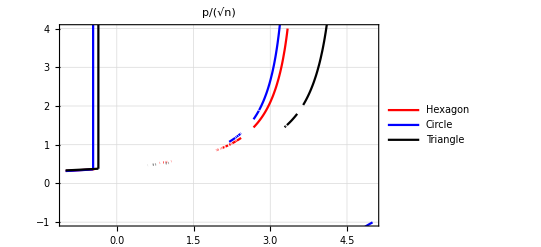

```mathematica
p1 = Plot[{Chop[{rb1,rb2,rb3}]}/.lw-> 1/.n-> 2.25*10^2/.bc->2 √2 3^(1/4)/.g-> 1/0.41,{b,-1,5},PlotStyle->{{Red},{Red},{Dashed}},PlotRange->{-1,4},PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
p2 = Plot[{Chop[{rb1,rb2,rb3}]}/.lw-> 1/.n-> 2.25*10^2/.bc->2 √π/.g->  1/0.41,{b,-1,5},PlotStyle->Blue,PlotLegends-> {"Circle"}];
p3 = Plot[{Chop[{rb1,rb2,rb3}]}/.lw-> 1/.n-> 2.25*10^2/.bc->2 3^(3/4)/.g->  1/0.41,{b,-1,5},PlotStyle->Black,PlotLegends-> {"Triangle"}];
Show[p1,p2,p3,PlotLabel->Style[p/Sqrt[n] (λ = 1),18],AxesLabel->{Style[β,16]},LabelStyle->Directive[Bold]]
```

```mathematica
1/Sqrt[1/(12 √3)]
```

2 3^(3/4)

```mathematica
N[2 3^(3/4)]
```

4.55901

```mathematica
N[2 √π]
```

3.54491

```mathematica
poly1 = a p (r p^2 - 1) + l
```

```mathematica
Solve[poly1==0,p]
```

{{p→((2/3)^(1/3) a)/((-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))+((-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))/(2^(1/3) 3^(2/3) a r)},{p→-((1+ⅈ √3) a)/(2^(2/3) 3^(1/3) (-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))-((1-ⅈ √3) (-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))/(2 2^(1/3) 3^(2/3) a r)},{p→-((1-ⅈ √3) a)/(2^(2/3) 3^(1/3) (-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))-((1+ⅈ √3) (-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))/(2 2^(1/3) 3^(2/3) a r)}}

```mathematica
((2/3)^(1/3) a)/((-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))+((-9 a^2 l r^2+√3 √(-4 a^6 r^3+27 a^4 l^2 r^4))^(1/3))/(2^(1/3) 3^(2/3) a r)/.a-> r/n*(g/2r+2)
```

((2/3)^(1/3) r (2+(g r)/2))/(n (-(9 l r^4 (2+(g r)/2)^2)/n^2+√3 √((27 l^2 r^8 (2+(g r)/2)^4)/n^4-(4 r^9 (2+(g r)/2)^6)/n^6))^(1/3))+(n (-(9 l r^4 (2+(g r)/2)^2)/n^2+√3 √((27 l^2 r^8 (2+(g r)/2)^4)/n^4-(4 r^9 (2+(g r)/2)^6)/n^6))^(1/3))/(2^(1/3) 3^(2/3) r^2 (2+(g r)/2))

```mathematica
Simplify[%98,{n>0,r>0,g>0}]
```

```mathematica
(4 3^(2/3) r^(1/3)+3^(2/3) g r^(4/3)+3^(1/3) (4+g r)^(1/3) (-9 l n+√3 √(27 l^2 n^2-r (4+g r)^2))^(2/3))/(3 (r (4+g r))^(2/3) (-9 l n+√3 √(27 l^2 n^2-r (4+g r)^2))^(1/3))
```

```mathematica
(4 3^(2/3) r^(1/3)+3^(2/3) g r^(4/3)+3^(1/3) (4+g r)^(1/3) (-9 l n+√3 √(27 l^2 n^2-r (4+g r)^2))^(2/3))/(3 (r (4+g r))^(2/3) (-9 l n+√3 √(27 l^2 n^2-r (4+g r)^2))^(1/3))/.g-> 1/.n-> 225
```

(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3) (-2025 l+√3 √(1366875 l^2-r (4+r)^2))^(2/3))/(3 (r (4+r))^(2/3) (-2025 l+√3 √(1366875 l^2-r (4+r)^2))^(1/3))

```mathematica
Simplify[(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3) (-2025 l+√3 √(1366875 l^2-r (4+r)^2))^(2/3))/(3 (r (4+r))^(2/3) (-2025 l+√3 √(1366875 l^2-r (4+r)^2))^(1/3))]
```

(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3) (-2025 l+√(4100625 l^2-3 r (4+r)^2))^(2/3))/(3 (r (4+r))^(2/3) (-2025 l+√(4100625 l^2-3 r (4+r)^2))^(1/3))

```mathematica
Manipulate[Plot[%108,{l,-8,8}],{g,0,2},{r,0.01,2},{n,1,225}]
```

```mathematica
(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3) (-2025 l+√(4100625 l^2-3 r (4+r)^2))^(1/3))/(3 (r (4+r))^(2/3))
```

```mathematica
(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3))/(3 (r (4+r))^(2/3))
```

((4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3)) (-2025 l+√(4100625 l^2-3 r (4+r)^2))^(1/3))/(3 (r (4+r))^(2/3))

```mathematica
(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3))/(3 (r (4+r))^(2/3))
```

(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3))/(3 (r (4+r))^(2/3))

```mathematica
Simplify[4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3)]
```

3^(1/3) (4 3^(1/3) r^(1/3)+3^(1/3) r^(4/3)+(4+r)^(1/3))

```mathematica
ExpandAll[(4 3^(2/3) r^(1/3)+3^(2/3) r^(4/3)+3^(1/3) (4+r)^(1/3))/(3 (r (4+r))^(2/3))]
```

```mathematica
((-2025 l+√(4100625 l^2-3 r (4+r)^2))^(1/3))/(3^(1/3)(4+r)^(1/3))(1/r^(1/3)(4/(4+r)^(1/3)+1/(3^(1/3) r^(1/3)))+r^(2/3)/(4+r)^(1/3))
```

((r^(2/3)/(4+r)^(1/3)+(1/(3^(1/3) r^(1/3))+4/(4+r)^(1/3))/r^(1/3)) (-2025 l+√(4100625 l^2-3 r (4+r)^2))^(1/3))/(3^(1/3) (4+r)^(1/3))

```mathematica
4100625 l^2-3 r (4+r)^2
```

4100625 l^2-3 r (4+r)^2

```mathematica
Manipulate[Plot[4100625 l^2-3 r (4+r)^2,{r,-0.03178118904542691,0.03178118904542691}],{l,-5.580236210994025*^-7,5.580236210994025*^-7}]
```

```mathematica
-4 a^6 r^3+27 a^4 l^2 r^4
```

-4 a^6 r^3+27 a^4 l^2 r^4

```mathematica
Simplify[-4 a^6 r^3+27 a^4 l^2 r^4]
```

```mathematica
a^4 r^3 (-4 a^2+27 l^2 r)/.a-> r/n*(g/2r+2)
```

(r^7 (2+(g r)/2)^4 (27 l^2 r-(4 r^2 (2+(g r)/2)^2)/n^2))/n^4

```mathematica
Simplify[(r^7 (2+(g r)/2)^4 (27 l^2 r-(4 r^2 (2+(g r)/2)^2)/n^2))/n^4]
```

-(r^8 (4+g r)^4 (-27 l^2 n^2+r (4+g r)^2))/(16 n^6)

```mathematica
Manipulate[Plot[Log[Abs[-(r^8 (4+g r)^4 (-27 l^2 n^2+r (4+g r)^2))/(16 n^6)]],{l,-1,1}],{g,0.0,1},{n,1,200},{r,0.01,2}]
```